```mathematica
Remove["Global`*"]
```

```mathematica
replacements={
Cos[ϕ]->cϕ,
Sin[ϕ]->sϕ,
Cos[θ]->cθ,
Sec[θ]->1/cθ,
Sin[θ]->sθ,
Tan[θ]->tθ,
Cos[ψ]->cψ,
Sin[ψ]->sψ,
Cos[ϕ/2]->chϕ,
Sin[ϕ/2]->shϕ,
Cos[θ/2]->chθ,
Sin[θ/2]->shθ,
Cos[ψ/2]->chψ,
Sin[ψ/2]->shψ,
Sin[Sqrt[x^2+y^2+z^2]/2]->shα,
Cos[Sqrt[x^2+y^2+z^2]/2]->chα,
x^2+y^2+z^2->α^2,
w^2->ws,
x^2->xs,
y^2->ys,
z^2->zs
};
```

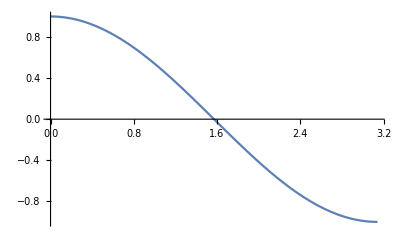

```mathematica
Plot[Cos[w],{w,0,π}]
```

```mathematica
Limit[2ArcCos[w]/Sqrt[1-w^2],w->1,Direction->"FromBelow"]
Limit[2ArcCos[w]/Sqrt[1-w^2],w->-1,Direction->"FromAbove"]
Series[2ArcCos[1-x],{x,0,1}]
```

2

∞

2 √2 √x+O[x]^(3/2)

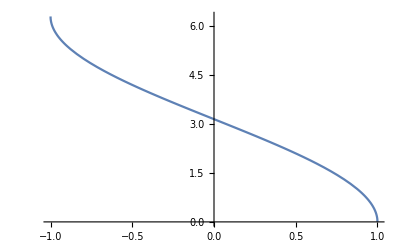

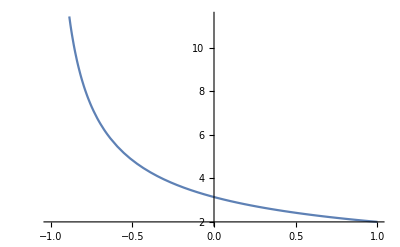

```mathematica
Plot[2ArcCos[w],{w,-1,1}]
Plot[2ArcCos[w]/Sqrt[1-w^2],{w,-1,1}]
```

```mathematica
Inverse[DiagonalMatrix[{3,5,7}]]
DiagonalMatrix[{3,5,7}]DiagonalMatrix[{3,5,7}]
```

{{1/3,0,0},{0,1/5,0},{0,0,1/7}}

{{9,0,0},{0,25,0},{0,0,49}}

```mathematica
Form[expr_]:=Simplify[ReplaceAll[expr,replacements],{α>0,a==-2shα+chα α}];
MForm[expr_]:=MatrixForm[Form[expr]];
TForm[expr_]:=MatrixForm[Map[MatrixForm,Form[expr]]];
JForm[expr_]:=CForm[Form[expr]];
MJForm[expr_]:=Column[{MForm[expr],JForm[expr]}];
TJForm[expr_]:=Column[{TForm[expr],JForm[expr]}];
```

```mathematica
R2[θ_]:={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
MForm[R2[θ]]
dR2dθ[θ_]:=D[R2[θ],{θ}];
MForm[dR2dθ[θ]]
Integrate[R2[θ],{θ,a,b}]
dR2dθ[a]-dR2dθ[b]==Integrate[R2[θ],{θ,a,b}]
F[θ_]:=Transpose[R2[θ]].{Subscript[FB, x],Subscript[FB, y]};
v[t_]:=Simplify[{Subscript[v, x],Subscript[v, y]}+Integrate[F[Subscript[θ, 0]+ω t]/mass,{t,0,t}]];
v[t]
d[t_]:=Simplify[{Subscript[d, x],Subscript[d, y]}+Integrate[v[t],{t,0,t}]];
d[t]
```

(cθ | sθ
-sθ | cθ)

(-sθ | cθ
-cθ | -sθ)

{{-Sin[a]+Sin[b],Cos[a]-Cos[b]},{-Cos[a]+Cos[b],-Sin[a]+Sin[b]}}

True

{(2 Sin[(t ω)/2] (Cos[(t ω)/2+θ_0] FB_x-Sin[(t ω)/2+θ_0] FB_y))/(mass ω)+v_x,(2 Sin[(t ω)/2] (Sin[(t ω)/2+θ_0] FB_x+Cos[(t ω)/2+θ_0] FB_y))/(mass ω)+v_y}

{d_x+(-(-Cos[θ_0]+Cos[t ω+θ_0]+t ω Sin[θ_0]) FB_x+(-t ω Cos[θ_0]-Sin[θ_0]+Sin[t ω+θ_0]) FB_y+mass t ω^2 v_x)/(mass ω^2),d_y+((t ω Cos[θ_0]+Sin[θ_0]-Sin[t ω+θ_0]) FB_x-(-Cos[θ_0]+Cos[t ω+θ_0]+t ω Sin[θ_0]) FB_y+mass t ω^2 v_y)/(mass ω^2)}

```mathematica
N[Expand[F[2 Pi/100]*0.4]]
Integrate[F[θ],{θ,0,2 Pi/100}]
N[Expand[Integrate[F[θ],{θ,0,2 Pi/100}]*0.4/(2 Pi/100)]]
```

{0.399211 FB_x-0.0251162 FB_y,0.0251162 FB_x+0.399211 FB_y}

{Sin[π/50] FB_x-2 Sin[π/100]^2 FB_y,2 Sin[π/100]^2 FB_x+Sin[π/50] FB_y}

{0.399737 FB_x-0.0125622 FB_y,0.0125622 FB_x+0.399737 FB_y}

```mathematica
TransposeIJ[expr_]:=Transpose[expr];
TransposeJK[expr_]:=Map[Transpose,expr];
```

```mathematica
LimitU[f_]:=
Normal[Series[
Normal[Series[
Normal[Series[
f[{ϕ,θ,ψ}]
,{ϕ,0,1}]]
,{θ,0,1}]]
,{ψ,0,1}]];
LimitV[f_]:=
Normal[Series[
Normal[Series[
Normal[Series[
f[{x,y,z}]
,{x,0,1}]]
,{y,0,1}]]
,{z,0,1}]];
LimitUQ[f_]:=
Normal[Series[
Normal[Series[
Normal[Series[
Normal[Series[
f[{w,x,y,z}]
,{w,0,1}]]
,{x,0,1}]]
,{y,0,1}]]
,{z,0,1}]];
LimitUQ[f_]:=
Normal[Series[
Normal[Series[
Normal[Series[
f[{Sqrt[1-x^2-y^2-z^2],x,y,z}]
,{x,0,1}]]
,{y,0,1}]]
,{z,0,1}]];
LimitUQW[f_]:=
Normal[Series[
f[{w,x,y,z}]
,{w,1,1}]];
```

```mathematica
Rϕ[ϕ_]:=Transpose[EulerMatrix[{ϕ,0,0},{1,2,3}]];
MForm[Rϕ[ϕ]]
Rθ[θ_]:=Transpose[EulerMatrix[{0,θ,0},{1,2,3}]];
MForm[Rθ[θ]]
Rψ[ψ_]:=Transpose[EulerMatrix[{0,0,ψ},{1,2,3}]];
MForm[Rψ[ψ]]
```

(1 | 0 | 0
0 | cϕ | sϕ
0 | -sϕ | cϕ)

(cθ | 0 | -sθ
0 | 1 | 0
sθ | 0 | cθ)

(cψ | sψ | 0
-sψ | cψ | 0
0 | 0 | 1)

```mathematica
R3[{ϕ_,θ_,ψ_}]:=Rϕ[ϕ].Rθ[θ].Rψ[ψ];
MJForm[R[{ϕ,θ,ψ}]]
```

R[{ϕ,θ,ψ}]
R(List(ϕ,θ,ψ))

```mathematica
LR3[{ϕ_,θ_,ψ_}]:=LimitU[R3];
MForm[LR3[{ϕ,θ,ψ}]]
```

(1 | ψ | -θ
θ ϕ-ψ | 1+θ ϕ ψ | ϕ
θ+ϕ ψ | -ϕ+θ ψ | 1)

```mathematica
dR3dϕ[{ϕ_,θ_,ψ_}]:=D[R3[{ϕ,θ,ψ}],{ϕ}];
MForm[dR3dϕ[{ϕ,θ,ψ}]]
dR3dθ[{ϕ_,θ_,ψ_}]:=D[R3[{ϕ,θ,ψ}],{θ}];
MForm[dR3dθ[{ϕ,θ,ψ}]]
dR3dψ[{ϕ_,θ_,ψ_}]:=D[R3[{ϕ,θ,ψ}],{ψ}];
MForm[dR3dψ[{ϕ,θ,ψ}]]
```

(0 | 0 | 0
cϕ cψ sθ+sϕ sψ | -cψ sϕ+cϕ sθ sψ | cθ cϕ
-cψ sθ sϕ+cϕ sψ | -cϕ cψ-sθ sϕ sψ | -cθ sϕ)

(-cψ sθ | -sθ sψ | -cθ
cθ cψ sϕ | cθ sϕ sψ | -sθ sϕ
cθ cϕ cψ | cθ cϕ sψ | -cϕ sθ)

(-cθ sψ | cθ cψ | 0
-cϕ cψ-sθ sϕ sψ | cψ sθ sϕ-cϕ sψ | 0
cψ sϕ-cϕ sθ sψ | cϕ cψ sθ+sϕ sψ | 0)

```mathematica
dR3du[{ϕ_,θ_,ψ_}]:=D[R3[{ϕ,θ,ψ}],{{ϕ,θ,ψ}}];
TJForm[dR3du[{ϕ,θ,ψ}]]
```

((0 | -cψ sθ | -cθ sψ
0 | -sθ sψ | cθ cψ
0 | -cθ | 0)
(cϕ cψ sθ+sϕ sψ | cθ cψ sϕ | -cϕ cψ-sθ sϕ sψ
-cψ sϕ+cϕ sθ sψ | cθ sϕ sψ | cψ sθ sϕ-cϕ sψ
cθ cϕ | -sθ sϕ | 0)
(-cψ sθ sϕ+cϕ sψ | cθ cϕ cψ | cψ sϕ-cϕ sθ sψ
-cϕ cψ-sθ sϕ sψ | cθ cϕ sψ | cϕ cψ sθ+sϕ sψ
-cθ sϕ | -cϕ sθ | 0))
List(List(List(0,-(cψ*sθ),-(cθ*sψ)),List(0,-(sθ*sψ),cθ*cψ),List(0,-cθ,0)),List(List(cϕ*cψ*sθ + sϕ*sψ,cθ*cψ*sϕ,-(cϕ*cψ) - sθ*sϕ*sψ),List(-(cψ*sϕ) + cϕ*sθ*sψ,cθ*sϕ*sψ,cψ*sθ*sϕ - cϕ*sψ),List(cθ*cϕ,-(sθ*sϕ),0)),List(List(-(cψ*sθ*sϕ) + cϕ*sψ,cθ*cϕ*cψ,cψ*sϕ - cϕ*sθ*sψ),List(-(cϕ*cψ) - sθ*sϕ*sψ,cθ*cϕ*sψ,cϕ*cψ*sθ + sϕ*sψ),List(-(cθ*sϕ),-(cϕ*sθ),0)))

```mathematica
TForm[TransposeIJ[TransposeJK[D[R3[{ϕ,θ,ψ}],{{ϕ,θ,ψ}}]]]]
```

((0 | 0 | 0
cϕ cψ sθ+sϕ sψ | -cψ sϕ+cϕ sθ sψ | cθ cϕ
-cψ sθ sϕ+cϕ sψ | -cϕ cψ-sθ sϕ sψ | -cθ sϕ)
(-cψ sθ | -sθ sψ | -cθ
cθ cψ sϕ | cθ sϕ sψ | -sθ sϕ
cθ cϕ cψ | cθ cϕ sψ | -cϕ sθ)
(-cθ sψ | cθ cψ | 0
-cϕ cψ-sθ sϕ sψ | cψ sθ sϕ-cϕ sψ | 0
cψ sϕ-cϕ sθ sψ | cϕ cψ sθ+sϕ sψ | 0))

```mathematica
Eu[{ϕ_,θ_,ψ_}]:=
{
{Cos[θ]Cos[ψ],-Sin[ψ],0},
{Cos[θ]Sin[ψ],Cos[ψ],0},
{-Sin[θ],0,1}
};
MForm[Eu[{ϕ,θ,ψ}]]
cEu[{ϕ_,θ_,ψ_}]:=
{
{1,0,-Sin[θ]},
{0,Cos[ϕ],Cos[θ]Sin[ϕ]},
{0,-Sin[ϕ],Cos[θ]Cos[ϕ]}
};
MForm[cEu[{ϕ,θ,ψ}]]
icEu[{ϕ_,θ_,ψ_}]:=Simplify[Inverse[cEu[{ϕ,θ,ψ}]]];
MForm[icEu[{ϕ,θ,ψ}]]
```

(cθ cψ | -sψ | 0
cθ sψ | cψ | 0
-sθ | 0 | 1)

(1 | 0 | -sθ
0 | cϕ | cθ sϕ
0 | -sϕ | cθ cϕ)

(1 | sϕ tθ | cϕ tθ
0 | cϕ | -sϕ
0 | sϕ/cθ | cϕ/cθ)

```mathematica
dicEudu[{ϕ_,θ_,ψ_}]:=D[icEu[{ϕ,θ,ψ}],{{ϕ,θ,ψ}}];
TJForm[dicEudu[{ϕ,θ,ψ}]]
```

((0 | 0 | 0
cϕ tθ | sϕ/cθ^2 | 0
-sϕ tθ | cϕ/cθ^2 | 0)
(0 | 0 | 0
-sϕ | 0 | 0
-cϕ | 0 | 0)
(0 | 0 | 0
cϕ/cθ | (sϕ tθ)/cθ | 0
-sϕ/cθ | (cϕ tθ)/cθ | 0))
List(List(List(0,0,0),List(cϕ*tθ,sϕ/Power(cθ,2),0),List(-(sϕ*tθ),cϕ/Power(cθ,2),0)),List(List(0,0,0),List(-sϕ,0,0),List(-cϕ,0,0)),List(List(0,0,0),List(cϕ/cθ,(sϕ*tθ)/cθ,0),List(-(sϕ/cθ),(cϕ*tθ)/cθ,0)))

```mathematica
qa[α_,{x_,y_,z_}]:={Cos[α/2],x Sin[α/2],y Sin[α/2],z Sin[α/2]};
MForm[qa[α,{x,y,z}]]
qu[{ϕ_,θ_,ψ_}]:=
{
Cos[θ/2] Cos[ϕ/2] Cos[ψ/2]+Sin[θ/2] Sin[ϕ/2] Sin[ψ/2],Cos[θ/2] Cos[ψ/2] Sin[ϕ/2]-Cos[ϕ/2] Sin[θ/2] Sin[ψ/2],Cos[ϕ/2] Cos[ψ/2] Sin[θ/2]+Cos[θ/2] Sin[ϕ/2] Sin[ψ/2],-Cos[ψ/2] Sin[θ/2] Sin[ϕ/2]+Cos[θ/2] Cos[ϕ/2] Sin[ψ/2]
};
MJForm[qu[{ϕ,θ,ψ}]]
```

(Cos[α/2]
x Sin[α/2]
y Sin[α/2]
z Sin[α/2])

(chθ chϕ chψ+shθ shϕ shψ
chθ chψ shϕ-chϕ shθ shψ
chϕ chψ shθ+chθ shϕ shψ
-chψ shθ shϕ+chθ chϕ shψ)
List(chθ*chϕ*chψ + shθ*shϕ*shψ,chθ*chψ*shϕ - chϕ*shθ*shψ,chϕ*chψ*shθ + chθ*shϕ*shψ,-(chψ*shθ*shϕ) + chθ*chϕ*shψ)

```mathematica
qm[{pw_,px_,py_,pz_},{qw_,qx_,qy_,qz_}]:=
{
pw qw-px qx-py qy-pz qz,
pw qx+px qw-py qz+pz qy,
pw qy+px qz+py qw-pz qx,
pw qz-px qy+py qx+pz qw
};
MForm[qm[{pw,px,py,pz} , {qw,qx,qy,qz}]]
```

(pw qw-px qx-py qy-pz qz
px qw+pw qx+pz qy-py qz
py qw-pz qx+pw qy+px qz
pz qw+py qx-px qy+pw qz)

```mathematica
{qw,qx,qy,qz}+qm[{qw,qx,qy,qz},{0,wxt,wyt,wzt}]/2
Simplify[{qw,qx,qy,qz}+qm[{qw,qx,qy,qz},{0,0.01,0.02,0.03}]/2]
```

{qw+1/2 (-qx wxt-qy wyt-qz wzt),qx+1/2 (qw wxt+qz wyt-qy wzt),qy+1/2 (-qz wxt+qw wyt+qx wzt),qz+1/2 (qy wxt-qx wyt+qw wzt)}

{qw-0.005 qx-0.01 qy-0.015 qz,0.005 qw+qx-0.015 qy+0.01 qz,0.01 qw+0.015 qx+qy-0.005 qz,0.015 qw-0.01 qx+0.005 qy+qz}

```mathematica
Simplify[Normal[Series[
Simplify[Normal[Series[
Simplify[Normal[Series[
qm[{qw,qx,qy,qz},qv[{wxt,wyt,wzt}]]
,{wxt,0,1}]]]
,{wyt,0,1}]]]
,{wzt,0,1}]], {wzt>0}]
qm[{qw,qx,qy,qz},qv[{0.01,0.02,0.03}]]
```

{qw Cos[wzt/2]-((qx wxt+qy wyt+qz wzt) Sin[wzt/2])/wzt,qx Cos[wzt/2]+((qw wxt+qz wyt-qy wzt) Sin[wzt/2])/wzt,qy Cos[wzt/2]+((-qz wxt+qw wyt+qx wzt) Sin[wzt/2])/wzt,qz Cos[wzt/2]+((qy wxt-qx wyt+qw wzt) Sin[wzt/2])/wzt}

{0.999825 qw-0.00499971 qx-0.00999942 qy-0.0149991 qz,0.00499971 qw+0.999825 qx-0.0149991 qy+0.00999942 qz,0.00999942 qw+0.0149991 qx+0.999825 qy-0.00499971 qz,0.0149991 qw-0.00999942 qx+0.00499971 qy+0.999825 qz}

```mathematica
MJForm[qm[qm[qa[ϕ,{1,0,0}],qa[θ,{0,1,0}]],qa[ψ,{0,0,1}]]]
```

(chθ chϕ chψ+shθ shϕ shψ
chθ chψ shϕ-chϕ shθ shψ
chϕ chψ shθ+chθ shϕ shψ
-chψ shθ shϕ+chθ chϕ shψ)
List(chθ*chϕ*chψ + shθ*shϕ*shψ,chθ*chψ*shϕ - chϕ*shθ*shψ,chϕ*chψ*shθ + chθ*shϕ*shψ,-(chψ*shθ*shϕ) + chθ*chϕ*shψ)

```mathematica
qu[{ϕ,θ,ψ}]===qm[qm[qa[ϕ,{1,0,0}],qa[θ,{0,1,0}]],qa[ψ,{0,0,1}]]
```

True

```mathematica
Lqu [{ϕ_,θ_,ψ_}]:=LimitU[qu];
MForm[Lqu[{ϕ,θ,ψ}]]
```

(1+(θ ϕ ψ)/8
1/4 (2 ϕ-θ ψ)
1/4 (2 θ+ϕ ψ)
1/4 (-θ ϕ+2 ψ))

```mathematica
dqudu[{ϕ_,θ_,ψ_}]:=D[qu[{ϕ,θ,ψ}],{{ϕ,θ,ψ}}];
MForm[2dqudu[{ϕ,θ,ψ}]]
```

(-chθ chψ shϕ+chϕ shθ shψ | -chϕ chψ shθ+chθ shϕ shψ | chψ shθ shϕ-chθ chϕ shψ
chθ chϕ chψ+shθ shϕ shψ | -chψ shθ shϕ-chθ chϕ shψ | -chϕ chψ shθ-chθ shϕ shψ
-chψ shθ shϕ+chθ chϕ shψ | chθ chϕ chψ-shθ shϕ shψ | chθ chψ shϕ-chϕ shθ shψ
-chϕ chψ shθ-chθ shϕ shψ | -chθ chψ shϕ-chϕ shθ shψ | chθ chϕ chψ+shθ shϕ shψ)

```mathematica
Q[{w_,x_,y_,z_}]:=
{
{w,-x,-y,-z},
{x,w,z,-y},
{y,-z,w,x},
{z,y,-x,w}
};
cQ[{w_,x_,y_,z_}]:=
{
{w,-x,-y,-z},
{x,w,-z,y},
{y,z,w,-x},
{z,-y,x,w}
};
```

```mathematica
αv[{x_,y_,z_}]:=Sqrt[x^2+y^2+z^2];
nv[{x_,y_,z_}]:={x,y,z}/αv[{x,y,z}];
αq[{w_,x_,y_,z_}]:=2ArcCos[w];
nq[{w_,x_,y_,z_}]:={x,y,z}/Sqrt[1-w^2];
```

```mathematica
vq[{w_,x_,y_,z_}]:=αq[{w,x,y,z}]nq[{w,x,y,z}];
vq[{w,x,y,z}]
```

{(2 x ArcCos[w])/(√(1-w^2)),(2 y ArcCos[w])/(√(1-w^2)),(2 z ArcCos[w])/(√(1-w^2))}

```mathematica
Lvq=LimitUQ[vq];
MForm[Simplify[Lvq,{z>0}]]
```

(2 x
2 y
2 z)

```mathematica
dvqdq[{w_,x_,y_,z_}]:=D[vq[{w,x,y,z}],{{w,x,y,z}}];
MJForm[dvqdq[{w,x,y,z}]]
```

(2 x (1/(-1+ws)+(w ArcCos[w])/(1-ws)^(3/2)) | (2 ArcCos[w])/(√(1-ws)) | 0 | 0
2 y (1/(-1+ws)+(w ArcCos[w])/(1-ws)^(3/2)) | 0 | (2 ArcCos[w])/(√(1-ws)) | 0
2 z (1/(-1+ws)+(w ArcCos[w])/(1-ws)^(3/2)) | 0 | 0 | (2 ArcCos[w])/(√(1-ws)))
List(List(2*x*(1/(-1 + ws) + (w*ArcCos(w))/Power(1 - ws,1.5)),(2*ArcCos(w))/Sqrt(1 - ws),0,0),List(2*y*(1/(-1 + ws) + (w*ArcCos(w))/Power(1 - ws,1.5)),0,(2*ArcCos(w))/Sqrt(1 - ws),0),List(2*z*(1/(-1 + ws) + (w*ArcCos(w))/Power(1 - ws,1.5)),0,0,(2*ArcCos(w))/Sqrt(1 - ws)))

```mathematica
Ldvqdq =Simplify[LimitUQW[dvqdq],{w<1}];
MForm[Ldvqdq]
```

(1/120 (94 w-3 (53+5 ws)) x | 2 | 0 | 0
1/120 (94 w-3 (53+5 ws)) y | 0 | 2 | 0
1/120 (94 w-3 (53+5 ws)) z | 0 | 0 | 2)

```mathematica
qv[{x_,y_,z_}]:=qa[αv[{x,y,z}],nv[{x,y,z}]];
MForm[qv[{x,y,z}]]
```

(chα
(shα x)/α
(shα y)/α
(shα z)/α)

```mathematica
dqvdv[{x_,y_,z_}]:=D[qv[{x,y,z}],{{x,y,z}}];
MJForm[2α^3 dqvdv[{x,y,z}]]
```

(-shα x α^2 | -shα y α^2 | -shα z α^2
a xs+2 shα α^2 | a x y | a x z
a x y | a ys+2 shα α^2 | a y z
a x z | a y z | a zs+2 shα α^2)
List(List(-(shα*x*Power(α,2)),-(shα*y*Power(α,2)),-(shα*z*Power(α,2))),List(a*xs + 2*shα*Power(α,2),a*x*y,a*x*z),List(a*x*y,a*ys + 2*shα*Power(α,2),a*y*z),List(a*x*z,a*y*z,a*zs + 2*shα*Power(α,2)))

```mathematica
Ldqvdv=Simplify[LimitV[dqvdv],{z>0}];
MForm[Ldqvdv]
```

(-(x Sin[z/2])/(2 z) | -(y Sin[z/2])/(2 z) | -1/2 Sin[z/2]
Sin[z/2]/z | (x y (z Cos[z/2]-2 Sin[z/2]))/(2 z^3) | (x (z Cos[z/2]-2 Sin[z/2]))/(2 z^2)
(x y (z Cos[z/2]-2 Sin[z/2]))/(2 z^3) | Sin[z/2]/z | (y (z Cos[z/2]-2 Sin[z/2]))/(2 z^2)
(x (z Cos[z/2]-2 Sin[z/2]))/(2 z^2) | (y (z Cos[z/2]-2 Sin[z/2]))/(2 z^2) | 1/2 Cos[z/2])

```mathematica
Rq[{w_,x_,y_,z_}]:=
{
{w^2+x^2-y^2-z^2,2x y+2w z,2x z-2w y},
{2x y-2w z,w^2-x^2+y^2-z^2,2y z+2w x},
{2x z+2w y,2y z-2w x,w^2-x^2-y^2+z^2}
};
```

```mathematica
dRqdq[{w_,x_,y_,z_}]:=D[Rq[{w,x,y,z}],{{w,x,y,z}}];
TJForm[dRqdq[{w,x,y,z}]/2]
```

((w | x | -y | -z
z | y | x | w
-y | z | -w | x)
(-z | y | x | -w
w | -x | y | -z
x | w | z | y)
(y | z | w | x
-x | -w | z | y
w | -x | -y | z))
List(List(List(w,x,-y,-z),List(z,y,x,w),List(-y,z,-w,x)),List(List(-z,y,x,-w),List(w,-x,y,-z),List(x,w,z,y)),List(List(y,z,w,x),List(-x,-w,z,y),List(w,-x,-y,z)))

```mathematica
uq[{w_,x_,y_,z_}]:={
ArcTan[2y z+2w x,z^2-y^2-x^2+w^2],
-ArcSin[2x z-2w y],
ArcTan[2x y+2w z,x^2+w^2-z^2-y^2]
};
MForm[uq[{w,x,y,z}]]
```

(ArcTan[2 w x+2 y z,ws-xs-ys+zs]
ArcSin[2 w y-2 x z]
ArcTan[2 x y+2 w z,ws+xs-ys-zs])

```mathematica
duqdq[{w_,x_,y_,z_}]:=D[uq[{w,x,y,z}],{{w,x,y,z}}];
TJForm[duqdq[{w,x,y,z}]]
```

(((2 (2 w (w x+y z)+x (-ws+xs+ys-zs)))/(4 (w x+y z)^2+(ws-xs-ys+zs)^2)
(2 (-2 x (w x+y z)+w (-ws+xs+ys-zs)))/(4 (w x+y z)^2+(ws-xs-ys+zs)^2)
(2 (-2 y (w x+y z)+z (-ws+xs+ys-zs)))/(4 (w x+y z)^2+(ws-xs-ys+zs)^2)
(2 (2 z (w x+y z)+y (-ws+xs+ys-zs)))/(4 (w x+y z)^2+(ws-xs-ys+zs)^2))
((2 y)/(√(1-4 (w y-x z)^2))
-(2 z)/(√(1-4 (w y-x z)^2))
(2 w)/(√(1-4 (w y-x z)^2))
-(2 x)/(√(1-4 (w y-x z)^2)))
((2 (2 w (x y+w z)+z (-ws-xs+ys+zs)))/(4 (x y+w z)^2+(ws+xs-ys-zs)^2)
(2 (2 x (x y+w z)+y (-ws-xs+ys+zs)))/(4 (x y+w z)^2+(ws+xs-ys-zs)^2)
(2 (-2 y (x y+w z)+x (-ws-xs+ys+zs)))/(4 (x y+w z)^2+(ws+xs-ys-zs)^2)
(2 (-2 z (x y+w z)+w (-ws-xs+ys+zs)))/(4 (x y+w z)^2+(ws+xs-ys-zs)^2)))
List(List((2*(2*w*(w*x + y*z) + x*(-ws + xs + ys - zs)))/(4*Power(w*x + y*z,2) + Power(ws - xs - ys + zs,2)),(2*(-2*x*(w*x + y*z) + w*(-ws + xs + ys - zs)))/(4*Power(w*x + y*z,2) + Power(ws - xs - ys + zs,2)),(2*(-2*y*(w*x + y*z) + z*(-ws + xs + ys - zs)))/(4*Power(w*x + y*z,2) + Power(ws - xs - ys + zs,2)),(2*(2*z*(w*x + y*z) + y*(-ws + xs + ys - zs)))/(4*Power(w*x + y*z,2) + Power(ws - xs - ys + zs,2))),List((2*y)/Sqrt(1 - 4*Power(w*y - x*z,2)),(-2*z)/Sqrt(1 - 4*Power(w*y - x*z,2)),(2*w)/Sqrt(1 - 4*Power(w*y - x*z,2)),(-2*x)/Sqrt(1 - 4*Power(w*y - x*z,2))),List((2*(2*w*(x*y + w*z) + z*(-ws - xs + ys + zs)))/(4*Power(x*y + w*z,2) + Power(ws + xs - ys - zs,2)),(2*(2*x*(x*y + w*z) + y*(-ws - xs + ys + zs)))/(4*Power(x*y + w*z,2) + Power(ws + xs - ys - zs,2)),(2*(-2*y*(x*y + w*z) + x*(-ws - xs + ys + zs)))/(4*Power(x*y + w*z,2) + Power(ws + xs - ys - zs,2)),(2*(-2*z*(x*y + w*z) + w*(-ws - xs + ys + zs)))/(4*Power(x*y + w*z,2) + Power(ws + xs - ys - zs,2))))